# EIWL Sections 45 and 46

## 4/8 Due to getting a little behind in the final two weeks of the semester, I only checked for completeness on PS 18-21. ~Brian

# PS 20 — Section 45 was accidentally included in Rania’s 4.18.2025 problem set, so I moved it here. See below.

## Section 45 ~ Disregard! I misread the github site - will put in next PSet

```mathematica
(* ok, I moved Section 45 into this new notebook, and called it PS20. However, you never sent Section 46. *)
```

```mathematica
planets=CloudGet["https://wolfr.am/7FxLgPm5"]
```

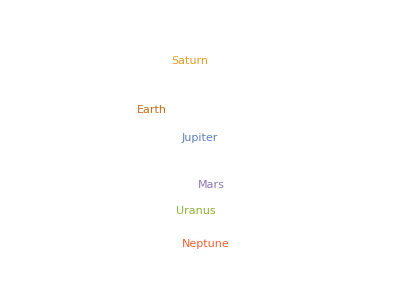

```mathematica
(*45.1 Make a word cloud of the planets,with weights determined by their number of moons.*)
WordCloud[Normal[planets[All,"Moons",Length]]]
```

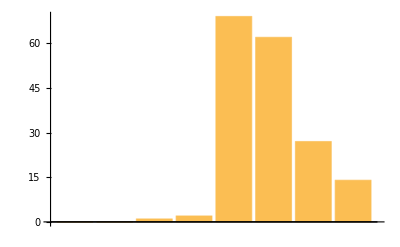

```mathematica
(*45.2 Make a bar chart of the number of moons for each planet.*)
BarChart[planets[All,"Moons",Length],ChartLabels->All]
```

```mathematica
(*45.3 Make a dataset of the masses of the planets,sorted by their number of moons*)
planets[SortBy[Length[#Moons]&],"Mass"]
```

```mathematica
(*45.4 Make a dataset of planets and the mass of each one’s most massive moon.*)
planets[All,"Moons",Max,"Mass"]
```

```mathematica
(*45.5 Make a dataset of masses of planets,where the planets are sorted by the largest mass of their moons.*)
planets[All,"Moons",Total,"Mass"][Sort]
```

```mathematica
(*45.6 Make a dataset of the median mass of all moons for each planet. *)
planets[All,"Moons",Median,"Mass"]
```

```mathematica
(*45. 7 For each planet,make a list of moons larger in mass than 0.0001 Earth masses*)
planets[All,"Moons",Select[]&][All, Keys]
```

Failure[…]

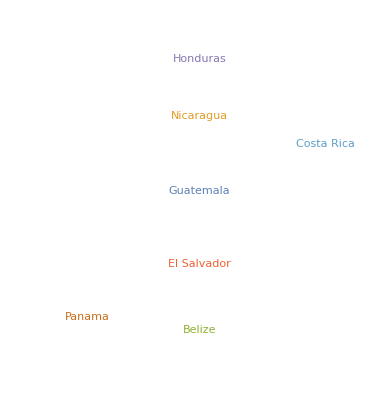

```mathematica
(*45.8 Make a word cloud of countries in Central America,with the names of countries proportional to the lengths of the Wikipedia article about them.*)
WordCloud[Association[#->StringLength[WikipediaData[#]]&/@EntityList[EntityClass["Country","CentralAmerica"]]]]
```